```mathematica
880
```

880

```mathematica
SetDirectory[NotebookDirectory[]]
```

\\z-sv-pool01\J.Wienand\Desktop\cs-imaging\heatmap\880normal

```mathematica
U21 = Import["U21.csv","csv"];
U23 = Import["U23.csv","csv"];
U35 = Import["U35.csv","csv"];
U41 = Import["U41.csv","csv"];
U64 = Import["U64.csv","csv"];
U51 = Import["U51.csv","csv"];
U65 = Import["U65.csv","csv"];
U75 = Import["U75.csv","csv"];
U27 = Import["U27.csv","csv"];
U26 = Import["U26.csv","csv"];
U34 = Import["U34.csv","csv"];
D12 = Import["D12.csv","csv"];
D21 = Import["D21.csv","csv"];
D23 = Import["D23.csv","csv"];
D35 = Import["D35.csv","csv"];
D41 = Import["D41.csv","csv"];
D64 = Import["D64.csv","csv"];
D51 = Import["D51.csv","csv"];
D65 = Import["D65.csv","csv"];
D75 = Import["D75.csv","csv"];
D27 = Import["D27.csv","csv"];
D26 = Import["D26.csv","csv"];
D34 = Import["D34.csv","csv"];
D15 = Import["D15.csv","csv"];
PathA = Import["A.csv","csv"];
PathB =  Import["B.csv","csv"];
PathC = Import["C.csv","csv"];
PathD = Import["D.csv","csv"];
PathE = Import["E.csv","csv"];;
PathF =  Import["F.csv","csv"];
PathR =  Import["R.csv","csv"]; (*red imaging closed transition*)
```

```mathematica
nmax = Length[U21[[1]]] - 1
```

8

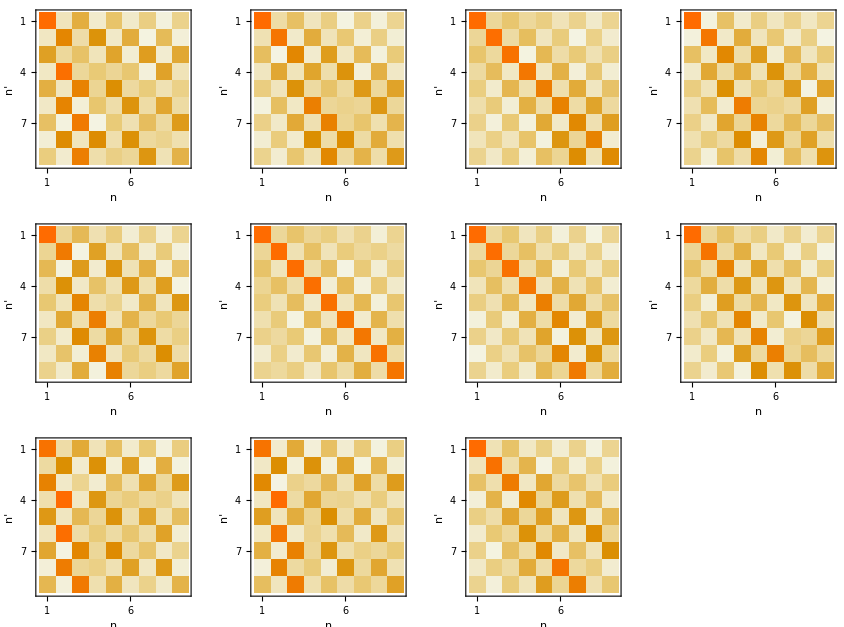

```mathematica
GraphicsGrid[{{MatrixPlot[U21,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 1"},{"n'",""}}],MatrixPlot[U23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[U35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[U41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[U64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[U51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[U65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[U75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[U27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[U26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[U34,FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
Total[U41[[All,2]]]
```

1.08579835995139654

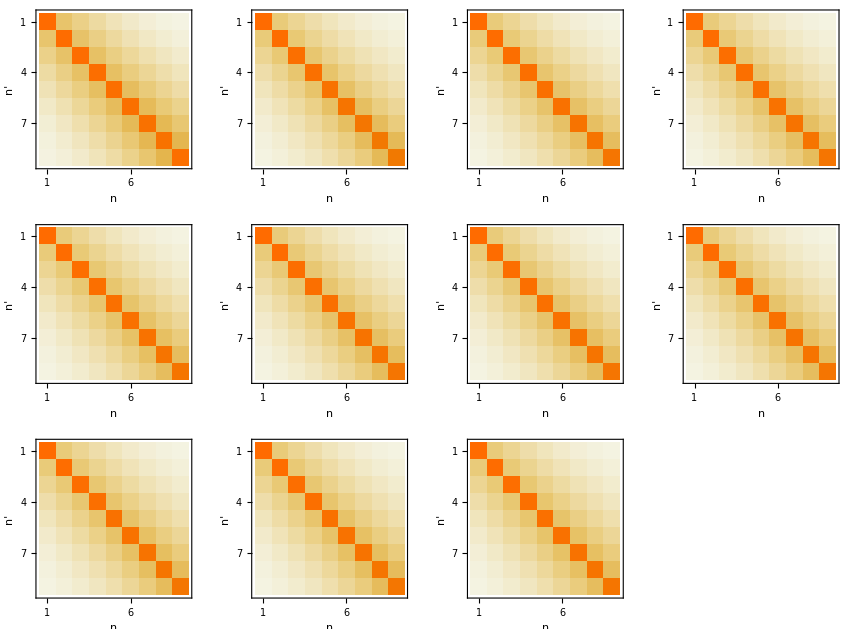

```mathematica
GraphicsGrid[{{MatrixPlot[D12,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","1 -> 2"},{"n'",""}}],MatrixPlot[D23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[D35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[D41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[D64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[D51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[D65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[D75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[D27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[D26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[D34,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
PathTot = 0.201004/(0.2001004+0.3678+0.25827)*PathA +0.3678/(0.2001004+0.3678+0.25827) PathB + 0.25827/(0.2001004+0.3678+0.25827) PathF;
PathTotE = 0.201004/(0.2001004+0.3678+0.25827+0.154494)*PathA +0.3678/(0.2001004+0.3678+0.25827+0.154494) PathB + 0.25827/(0.2001004+0.3678+0.25827+0.154494) PathF + 0.154494/(0.2001004+0.3678+0.25827 +0.154494)PathE;
(*+ +0.001969 PathC +0.016289PathD + 0.154494PathE ;*)
Paths ={PathA, PathB, PathC, PathD, PathE, PathF, PathTotE, PathTot, PathR};
```

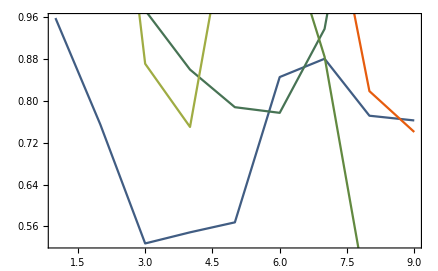

```mathematica
Show[{ListPlot[Table[Total[Table[Abs[PathA[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][1/8], Joined -> True, PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathB[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][2/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathC[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][3/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathD[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][4/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathE[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"]}[5/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathF[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"][6/8]},Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],
ListPlot[Table[Total[Table[Abs[PathR[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"][7/8]},Joined -> True,PlotTheme -> "Scientific",PlotRange-> All]
}]
```

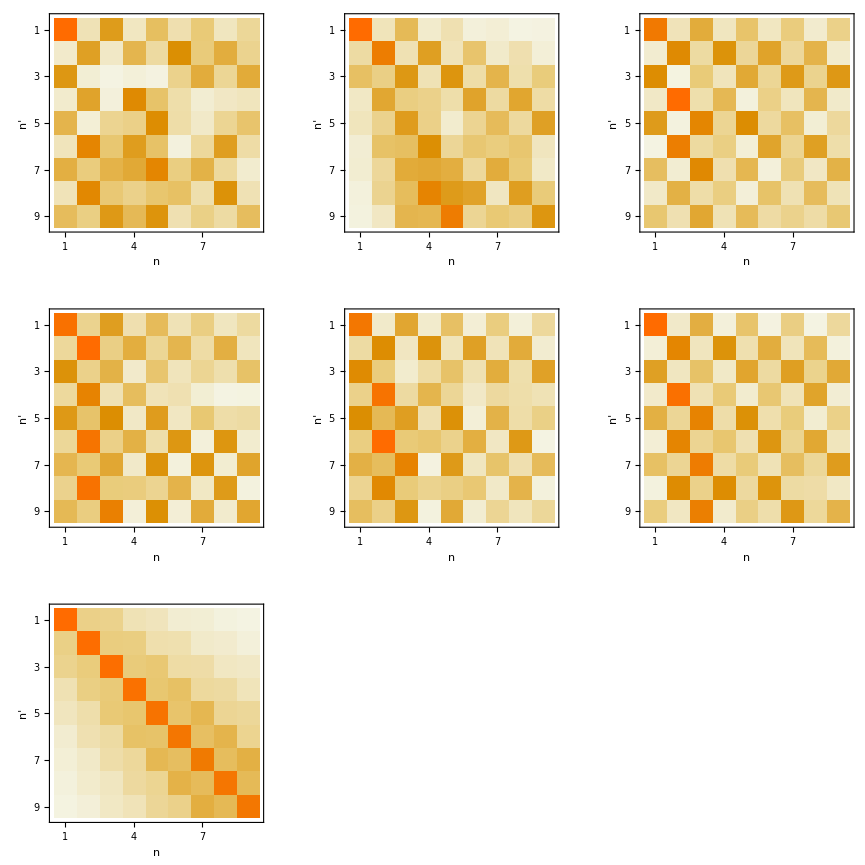

```mathematica
GraphicsGrid[{{MatrixPlot[PathA,FrameLabel -> {{"n","Path A: 2 -> 3 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathB,FrameLabel -> {{"n","Path B: 2 -> 3 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathC,FrameLabel -> {{"n","Path C: 2 -> 6 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}]
},
{MatrixPlot[PathD,FrameLabel -> {{"n","Path D: 2 -> 6 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathE,FrameLabel -> {{"n","Path E: 2 -> 7 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathF,FrameLabel -> {{"n","Path F: 2 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ]},{MatrixPlot[PathR,FrameLabel -> {{"n","Path Red Imaging: 1 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],None,None}}, FrameStyle-> Black]
```

```mathematica
Total[PathE[[2]]]
```

1.14270049757357823

```mathematica
tablePath[pa_]:=Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}]
tablePath[6]
tablePath[1]
tablePath[2]
tablePath[5]
```

{1.87323719630278659,3.97729707341228936,5.21934479316237399,3.69377709609714388,3.57124706928810424,4.60566465666176869,4.85364080751119341,4.02723628708666174,5.0424866794830794}

{2.52970064155569168,3.93478121944214885,2.74336919901722408,2.12499233738689846,2.70368356496393856,3.69630736626532894,3.84225626216408289,3.63809580364197163,3.4033525740392429}

{1.42158051599340874,3.04439334601344793,4.39718699430075603,4.4982351691384846,4.48035115087259415,3.56342340758678752,4.63936266091813399,7.4546104518440076,7.46306826266804547}

{2.59454935293732152,5.10539940572665187,4.76035543882562607,2.94315475765945218,4.78104701312991956,5.66691155259177594,5.09906153860757397,3.2014466185008572,2.82268860276532008}

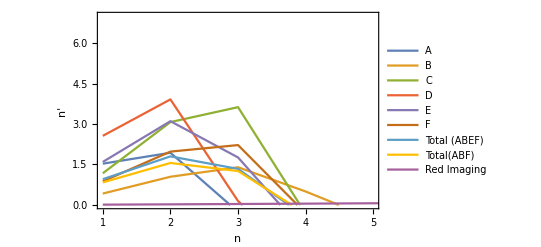

```mathematica
heatdata=Table[Table[Sum[Paths[[pa]][[r]][[ra]] ra,{ra,1,nmax+1}]-r,{r,1,Length[Paths[[pa]][[1,All]]]}],{pa,1,9}];
ListPlot[heatdata,PlotStyle -> ColorData["DarkRainbow"][pa/9],Joined -> True,FrameStyle -> Black, Frame -> True,PlotRange-> {{1,5},{0,7}}, FrameLabel->{"n", "n'"}, PlotLegends-> {"A","B","C","D","E","F","Total (ABEF)","Total(ABF)","Red Imaging"}]
```

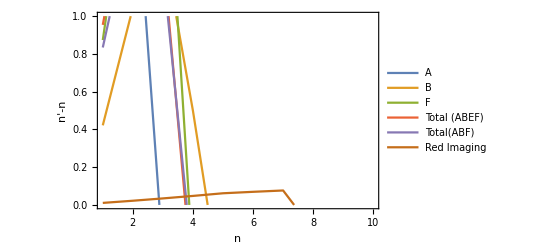

```mathematica
heatdata=Table[Table[Sum[Paths[[pa]][[r]][[ra]] ra,{ra,1,nmax+1}]-r,{r,1,Length[Paths[[pa]][[1,All]]]}],{pa,{1,2,6,7,8,9}}];
ListPlot[heatdata,PlotStyle -> ColorData["DarkRainbow"][pa/9],Joined -> True,FrameStyle -> Black, Frame -> True,PlotRange-> {{1,10},{0,1}}, FrameLabel->{"n", "n'-n"}, PlotLegends-> { "A","B","F","Total (ABEF)","Total(ABF)","Red Imaging"}]
```

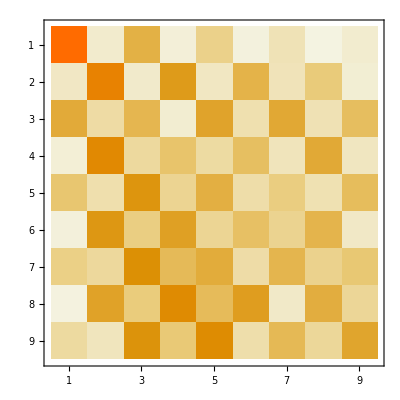

```mathematica
MatrixPlot[PathTot]
```

Multi-Experimente

```mathematica
intensities = Import["intensities.csv","csv"];
ldepthsomega =   Import["latticedepths1.csv","csv"];
heatings = Import["heatings.csv", "csv"];
totheating = 0.201004/(0.2001004+0.3678+0.25827)*heatings[[All,1]]+0.3678/(0.2001004+0.3678+0.25827) heatings[[All,2]] + 0.25827/(0.2001004+0.3678+0.25827) heatings[[All,6]];
totheatingE = 0.201004/(0.2001004+0.3678+0.25827+0.154494)*heatings[[All,1]]+0.3678/(0.2001004+0.3678+0.25827+0.154494) heatings[[All,2]] + 0.25827/(0.2001004+0.3678+0.25827+0.154494) heatings[[All,6]] + 0.154494/(0.2001004+0.3678+0.25827 +0.154494)heatings[[All,5]];
heatings2 = Import["heating2s.csv", "csv"];
totheating2 = 0.201004/(0.2001004+0.3678+0.25827)*heatings2[[All,1]]+0.3678/(0.2001004+0.3678+0.25827) heatings2[[All,2]] + 0.25827/(0.2001004+0.3678+0.25827) heatings2[[All,6]];
totheatingE2 = 0.201004/(0.2001004+0.3678+0.25827+0.154494)*heatings2[[All,1]]+0.3678/(0.2001004+0.3678+0.25827+0.154494) heatings2[[All,2]] + 0.25827/(0.2001004+0.3678+0.25827+0.154494) heatings2[[All,6]] + 0.154494/(0.2001004+0.3678+0.25827 +0.154494)heatings2[[All,5]];

heatingsext = Transpose[{heatings[[All,1]],heatings[[All,2]],heatings[[All,3]],heatings[[All,4]],heatings[[All,5]],heatings[[All,6]],heatings[[All,7]],totheating,totheatingE}];
heatingsext2 = Transpose[{heatings2[[All,1]],heatings2[[All,2]],heatings2[[All,3]],heatings2[[All,4]],heatings2[[All,5]],heatings2[[All,6]],heatings2[[All,7]],totheating2,totheatingE2}];
```

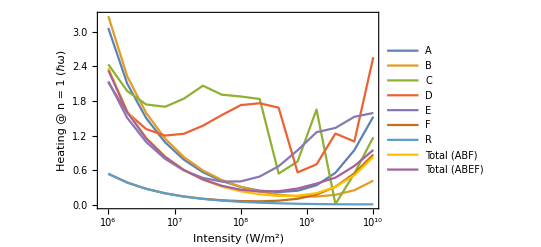

```mathematica
ListLogLinearPlot[Table[Thread[{Flatten[intensities], heatingsext[[All,in]]}],{in,1,9}], Joined -> True, PlotLegends-> {"A","B","C","D","E","F","R", "Total (ABF)", "Total (ABEF)"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Heating @ n = 1 (ℏω)"}]
```

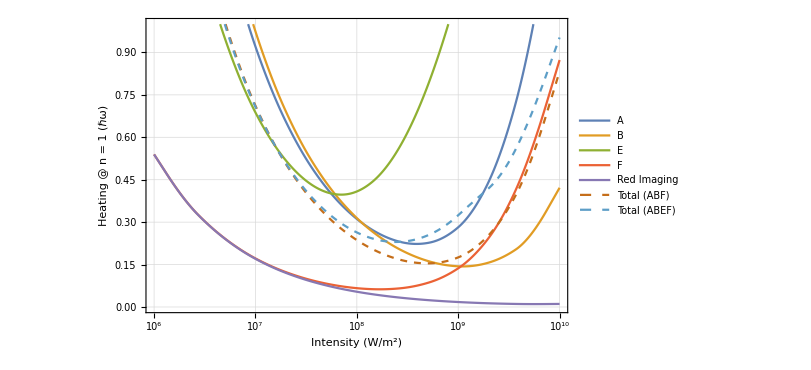

```mathematica
ListLogLinearPlot[Table[Thread[{Flatten[intensities], heatingsext[[All,in]]}],{in,{1,2,5,6,7,8,9}}], Joined -> True, PlotLegends-> {"A","B","E","F","Red Imaging", "Total (ABF)", "Total (ABEF)"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Heating @ n = 1 (ℏω)"}, PlotStyle ->{Normal,Normal,Normal,Normal,Normal,Dashed,Dashed}, Axes-> True, PlotRange -> {{10^6,10^10}, {0, 1}}, InterpolationOrder-> 2, ImageSize -> 600, GridLines -> Automatic]
```

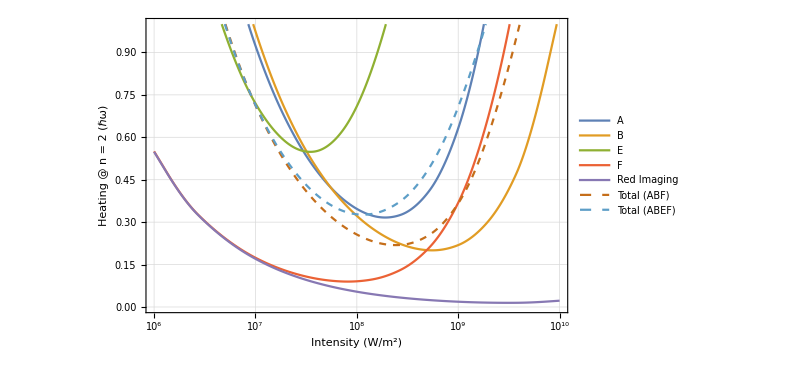

```mathematica
ListLogLinearPlot[Table[Thread[{Flatten[intensities], heatingsext2[[All,in]]}],{in,{1,2,5,6,7,8,9}}], Joined -> True, PlotLegends-> {"A","B","E","F","Red Imaging", "Total (ABF)", "Total (ABEF)"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Heating @ n = 2 (ℏω)"}, PlotStyle ->{Normal,Normal,Normal,Normal,Normal,Dashed,Dashed}, Axes-> True, PlotRange -> {{10^6,10^10}, {0, 1}}, InterpolationOrder-> 2, ImageSize -> 600, GridLines -> Automatic]
```

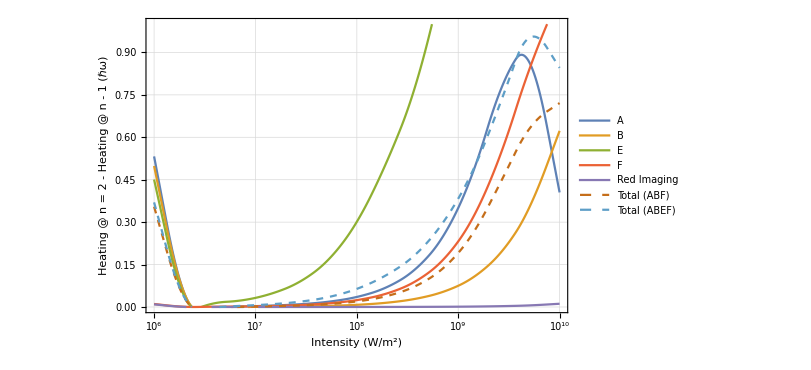

```mathematica
ListLogLinearPlot[Table[Thread[{Flatten[intensities], heatingsext2[[All,in]]-heatingsext[[All,in]]}],{in,{1,2,5,6,7,8,9}}], Joined -> True, PlotLegends-> {"A","B","E","F","Red Imaging", "Total (ABF)", "Total (ABEF)"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Heating @ n = 2 - Heating @ n - 1 (ℏω)"}, PlotStyle ->{Normal,Normal,Normal,Normal,Normal,Dashed,Dashed}, Axes-> True, PlotRange -> {{10^6,10^10}, {0, 1}}, InterpolationOrder-> 2, ImageSize -> 600, GridLines -> Automatic]
```

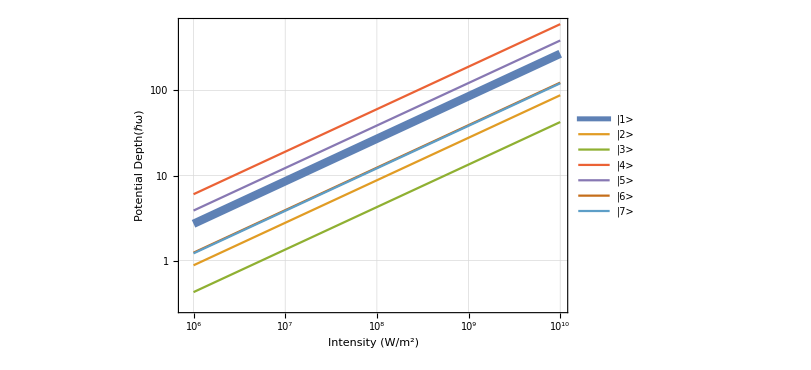

```mathematica
omegdepth = Table[Thread[{Flatten[intensities], ldepthsomega[[All,in]]}],{in,1,7}];
ListLogLogPlot[omegdepth, Joined -> True, PlotLegends-> {"|1>","|2>","|3>","|4>","|5>", "|6>", "|7>"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Potential Depth(ℏω)"}, PlotStyle ->{Thickness[0.01],Normal,Normal,Normal,Normal,Normal,Normal}, Axes-> True, PlotRange -> All, InterpolationOrder-> 3, ImageSize -> 600, GridLines -> Automatic]
```

```mathematica
ldepthsomega[[All,1]]
```

{2.70461188074568248,3.75804602232418317,5.22178801566634387,7.25565092034003101,10.0816942625567805,14.0084687534701704,19.4647042160136827,27.046118807456832,37.5804602232418006,52.2178801566634405,72.5565092034003811,100.816942625567791,140.084687534701715,194.647042160136692,270.46118807456827}

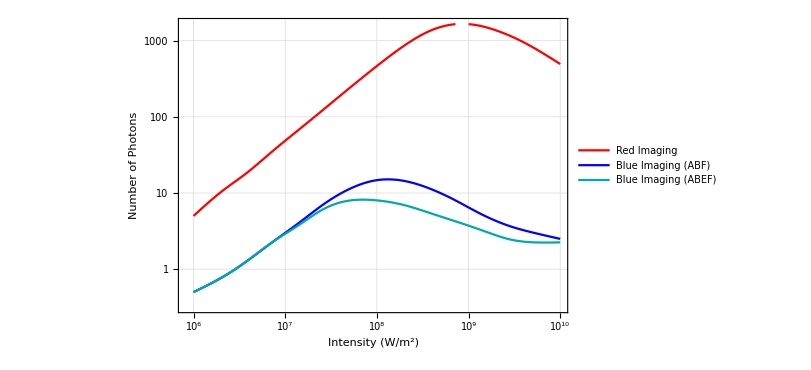

```mathematica
ListLogLogPlot[Table[Transpose[{Flatten[intensities], Table[h0 = heatingsext[[All,ind]][[z]]; m = Abs[(heatingsext2[[All,ind]][[z]]-heatingsext[[All,ind]][[z]])];
nra[nraalt_]:= nraalt+h0 + m*nraalt;
Count[Map[#<0.95*ldepthsomega[[All,1]][[z]]&,NestList[nra, 0,3000]], True]*If[ind> 7, 0.25, 1]
,{z,1, Length[intensities]}]}],{ind, {7,8,9}}] ,Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Number of Photons"},Joined -> True, Axes-> True, PlotRange -> All, InterpolationOrder-> 3, ImageSize -> 600, GridLines -> Automatic, PlotLegends -> {"Red Imaging", "Blue Imaging (ABF)", "Blue Imaging (ABEF)"}, PlotStyle -> {Red, Blue, Darker[Cyan]}]
```

```mathematica
880
```